# 1 DOF

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Get["MyPackage.wl"]
```

C:\Universita\MAGISTRALE\MasterThesis\Mathematica

```mathematica
ScientString[n_,dig_]:=ToString[ScientificForm[n,dig],TraditionalForm]
```

```mathematica
GetStep[vec_]:=Mean@Differences[vec]
```

```mathematica
colors={Blue,Red,Green};
```

```mathematica
opts={GridLines->Automatic,LabelStyle->{Black,Bold,FontFamily->"Times New Roman",FontSize->12},AxesStyle->{FontFamily->"Times New Roman"},Frame->True};
```

## Data and Model

```mathematica
alldata=Import["data.m"]
```

<|cellVal→{ν→0.3,Yp→2.5×10^9,ϵp→3.009×10^-11,ϵf→2.3895×10^-11,EBDp→303000000,EBDf→1.574×10^8,l0→1/40,w0→1/10,tp0→1/40000,tf0→1/100000,ξ0→3/1000,ϵ1max→0.05},tankVal→{d→5,Pt→50000,Vtank→1,Vftot→1,f→0.1},gasVal→{patm→101325,Tstd→288.15,γair→1.4,ρstdair→1.225,cv→717.2,cp→1.0042}|>

```mathematica
celldata=alldata["cellVal"]//N
```

{ν→0.3,Yp→2.5×10^9,ϵp→3.009×10^-11,ϵf→2.3895×10^-11,EBDp→3.03×10^8,EBDf→1.574×10^8,l0→0.025,w0→0.1,tp0→0.000025,tf0→0.00001,ξ0→0.003,ϵ1max→0.05}

```mathematica
Δtf=dtf/.Solve[((x-tf0)/2)/l0==(dtf/2)/(l0-(ξ-ξ0)),dtf][[1]]
```

-((tf0-x) (l0-ξ+ξ0))/l0

```mathematica
tf=tf0+Δtf;
```

```mathematica
pstraincond={ϵ1[x]->-1+√(1+((x-tf0)/(2 l0))^2),ϵ2[x]->0,ϵ3[x]->ϵ1[x] ν/(ν-1),σ1[x]->-Yp ϵ1[x]/(ν^2-1),σ2[x]->-Yp ν ϵ1[x]/(ν^2-1)};
pstresscond={ϵ1[x]->-1+√(1+((x-tf0)/(2 l0))^2),ϵ2[x]->-ϵ1[x] ν,ϵ3[x]->-ϵ1[x] ν,σ1[x]->Yp ϵ1[x]};
nostraincond={ϵ1[x]->0,ϵ2[x]->0,ϵ3[x]->0,σ1[x]->0,σ2[x]->0,σ3[x]->0};
```

```mathematica
computegeometry1[tf_]:=Module[{ltmp,tptmp,wtmp,Atmp,dAtmp,dCptmp,dCftmp,dCtmp,Ctmp,Volptmp,Volftmp,Voltmp},
ltmp=l0 (1+ϵ1[x]);
tptmp=tp0(1+ϵ3[x]);
wtmp=w0(1+ϵ2[x]);
Atmp=ltmp wtmp;
dAtmp=wtmp(1+ϵ1[x]);
dCptmp=(dAtmp ϵp)/tptmp;
dCftmp=(dAtmp ϵf)/tf;
dCtmp=(2/dCptmp+1/dCftmp)^(-1);
Ctmp=Integrate[dCtmp,ξ];
Ctmp=(Ctmp/. ξ->ξ0+l0)-(Ctmp/. ξ->ξ0)//Simplify;
Volptmp=2wtmp tptmp ltmp;
Volftmp=wtmp(2((x-tf0)/2 √(ltmp^2-((x-tf0)/2)^2))/2+ x ξ0);(*+tf0 √(ltmp^2-((x-tf0)/2)^2));*)
Voltmp=Volptmp+Volftmp;
{l->ltmp,tp->tptmp,w->wtmp,A->Atmp,dA->dAtmp,dCp->dCptmp,dCf->dCftmp,dC->dCtmp,CC->Ctmp,Volp->Volptmp,Volf->Volftmp,Vol->Voltmp}
]
```

```mathematica
geometry=computegeometry1[tf];
```

```mathematica
pstrain=Union[computegeometry1[tf]//.pstraincond,pstraincond];
pstress=Union[computegeometry1[tf]//.pstresscond,pstresscond];
nostrain=Union[computegeometry1[tf]//.nostraincond,nostraincond];
```

```mathematica
tolxmin=10^-10;
xmin=tf0+tolxmin/.celldata//N
xmaxth=x/.Solve[x>0&&((ϵ1[x]/.pstraincond)==ϵ1max)/.celldata,x][[1]]
```

0.0000100001

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.0160178

```mathematica
w0range=w0{0.5,1,1.5}/.celldata;
tp0range=tp0{0.5,1,1.5}/.celldata;
l0range=l0{0.5,1,1.5}/.celldata;
ξ0l0ratio=ξ0/l0/.celldata;
ξ0range=l0range ξ0l0ratio;
```

```mathematica
l0strings=Table[StringJoin["l_0 = " ,ScientString[l0range[[i]],3]," [m]"],{i,1,Length@l0range}];
tp0strings=Table[StringJoin["tp_0 = " ,ScientString[tp0range[[i]],3]," [m]"],{i,1,Length@tp0range}];
w0strings=Table[StringJoin["w_0 = " ,ScientString[w0range[[i]],3]," [m]"],{i,1,Length@w0range}];
ξ0strings=Table[StringJoin["ξ_0 = " ,ScientString[ξ0range[[i]],3],"[m]"],{i,1,Length@ξ0range}];
defstrings={"Plane strain","Plane stress","No strain"};
```

## Analysis

### Capacitance

```mathematica
Capac=CC/.pstrain
```

(l0 w0 √(1+(-tf0+x)^2/(4 l0^2)) ϵf (Log[l0 (2 tp0 ϵf+tf0 ϵp+(2 tp0 (-1+√(1+(-tf0+x)^2/(4 l0^2))) ϵf ν)/(-1+ν))]-Log[l0 (2 tp0 ϵf+x ϵp+(2 tp0 (-1+√(1+(-tf0+x)^2/(4 l0^2))) ϵf ν)/(-1+ν))]))/(tf0-x)

#### Different Deformations

```mathematica
Cdef={Capac/.pstrain,Capac/.pstress,Capac/.nostrain}/.celldata;
```

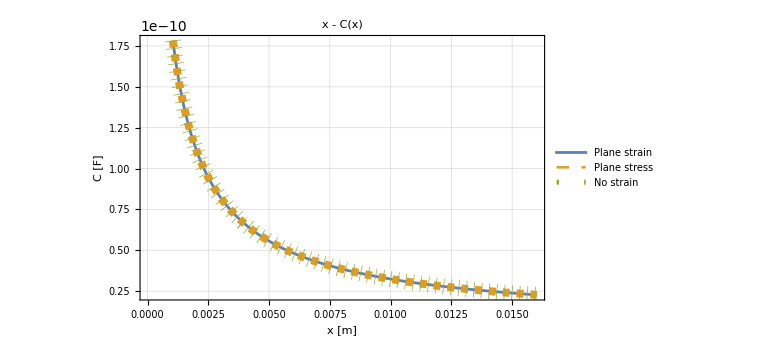

```mathematica
Plot[Cdef,{x,xmin,xmaxth},PlotStyle->{Automatic,{Dashed,Thickness@0.01},{Dotted,Thickness@0.02}},Evaluate@opts,FrameLabel->{"x [m]","C [F]"},PlotLabel->"x - C(x)",PlotLegends->defstrings,ImageSize->Large]
```

#### Geometry variation

```mathematica
Cl0=Capac/.l0->l0range/.celldata//Simplify;
Cw0=Capac/.w0->w0range/.celldata//Simplify;
Ctp0=Capac/.tp0->tp0range/.celldata//Simplify;
```

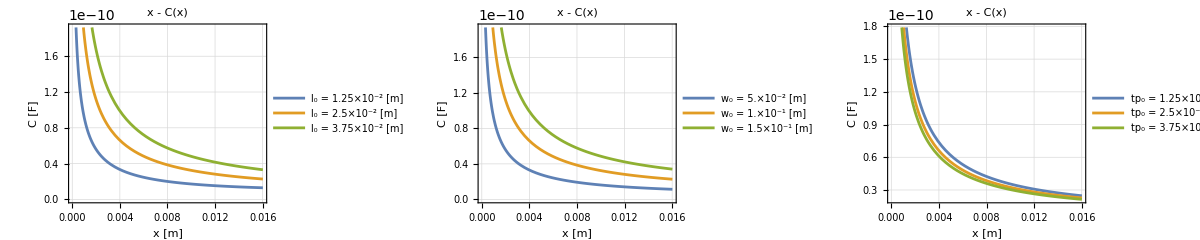

```mathematica
GraphicsRow[{
Plot[Cl0,{x,xmin,xmaxth},Evaluate@opts,FrameLabel->{"x [m]","C [F]"},PlotLabel->"x - C(x)",PlotLegends->{Placed[l0strings,{Center,Right}]}],
Plot[Cw0,{x,xmin,xmaxth},Evaluate@opts,FrameLabel->{"x [m]","C [F]"},PlotLabel->"x - C(x)",PlotLegends->{Placed[w0strings,{Center,Right}]}],
Plot[Ctp0,{x,xmin,xmaxth},Evaluate@opts,FrameLabel->{"x [m]","C [F]"},PlotLabel->"x - C(x)",PlotLegends->{Placed[tp0strings,{Center,Right}]}]
},ImageSize->Full]
```

### Max Voltage

```mathematica
Vmax=2 tp/ϵp Min[ϵp EBDp,ϵf EBDf]//Simplify;
```

#### Different deformation

```mathematica
Vmaxpepssig={Vmax//.pstrain,Vmax//.pstress}/.celldata;
```

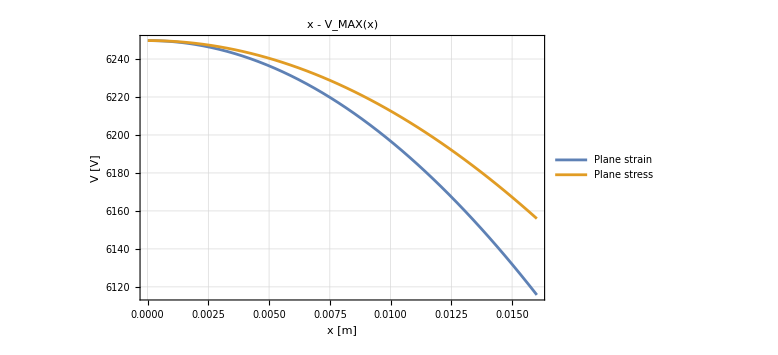

```mathematica
Plot[Vmaxpepssig,{x,xmin,xmaxth},Evaluate@opts,ImageSize->Large,FrameLabel->{"x [m]","V [V]"},PlotLabel->"x - V_MAX(x)",PlotLegends->defstrings]
```

#### l0 variation - Plane strain

```mathematica
Vmaxl0=Vmax/.pstrain/.l0->l0range/.celldata
```

{6249.71 (1-0.428571 (-1+√(1+1600. (-0.00001+x)^2))),6249.71 (1-0.428571 (-1+√(1+400. (-0.00001+x)^2))),6249.71 (1-0.428571 (-1+√(1+177.778 (-0.00001+x)^2)))}

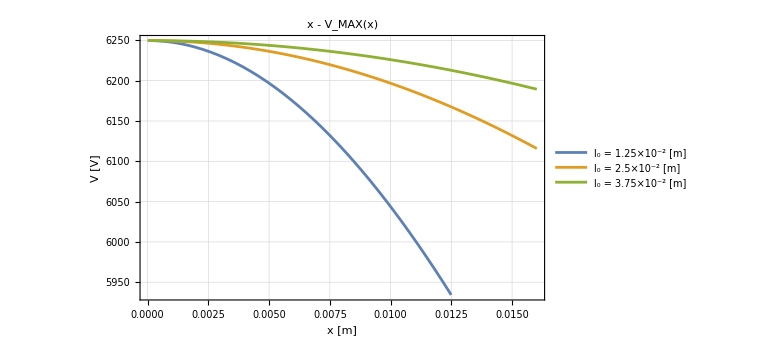

```mathematica
Plot[Vmaxl0,{x,xmin,xmaxth},Evaluate@opts,ImageSize->Large,FrameLabel->{"x [m]","V [V]"},PlotLabel->"x - V_MAX(x)",PlotLegends->l0strings]
```

### Pure elastic energy

```mathematica
pureUel=1/2 σ1[x] ϵ1[x] w tp l;
pureUelx={pureUel//.pstrain,pureUel//.pstress}/.celldata
```

{85.8516 (1-0.428571 (-1+√(1+400. (-0.00001+x)^2))) (-1+√(1+400. (-0.00001+x)^2))^2 √(1+400. (-0.00001+x)^2),78.125 (1-0.3 (-1+√(1+400. (-0.00001+x)^2)))^2 (-1+√(1+400. (-0.00001+x)^2))^2 √(1+400. (-0.00001+x)^2)}

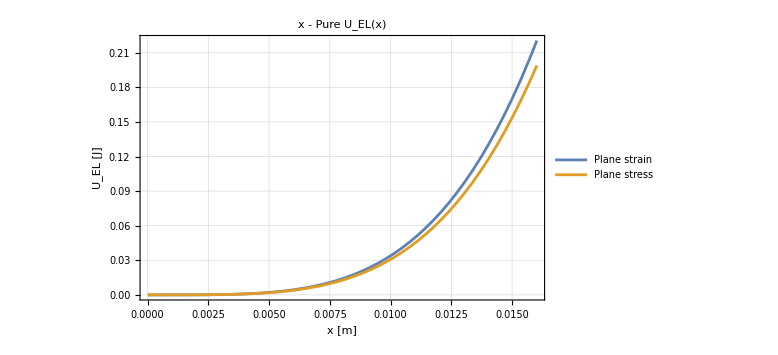

```mathematica
Plot[pureUelx,{x,xmin,xmaxth},Evaluate@opts,ImageSize->Large,FrameLabel->{"x [m]","U_EL [J]"},PlotLabel->"x - Pure U_EL(x)",PlotLegends->defstrings]
```

### Force

```mathematica
Fpstrain=D[pureUel//.pstrain,x]-V^2/2 D[CC/.pstrain,x]//Simplify;
```

```mathematica
Fpstrainl0=Fpstrain/.l0->l0range/.celldata;
```

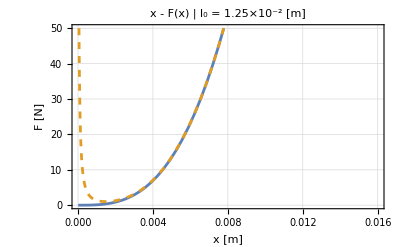
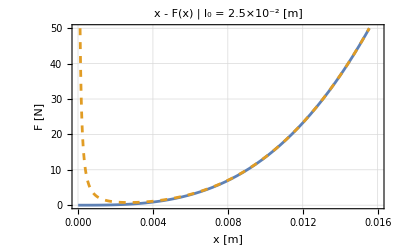
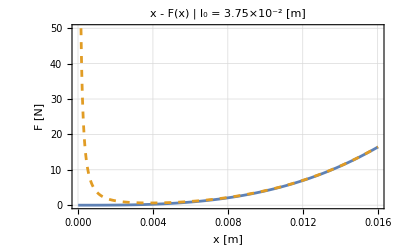

```mathematica
Row[
Flatten@Table[{
Plot[Evaluate@Table[Fpstrainl0[[i]]/.V->VV,{VV,{0,Vmaxl0[[i]]}}],{x,xmin,xmaxth},PlotStyle->{Automatic,Dashed},Evaluate@opts,PlotRangePadding->Scaled[0.01],PlotRange->{Automatic,{0,50}},FrameLabel->{"x [m]","F [N]"},PlotLabel->StringJoin["x - F(x) | ",l0strings[[i]]],ImageSize->400],Spacer@20},
{i,1,Length@l0range}]]
```

### Elastic energy from x - F

```mathematica
xrange=Range[xmin,0.5l0range,10^-5];
xrangenorm=xrange/l0range/.celldata;
```

```mathematica
Voll0=Vol//.pstrain/.{l0->l0range ,ξ0->ξ0range}/.celldata;
Volx=Table[Voll0[[i]]/.x->xrange[[i]],{i,1,Length@l0range}];
```

```mathematica
Uelx=Table[
ParallelTable[NIntegrate[(Fpstrainl0[[i]]/.V->Vmaxl0[[i]])-Fpstrainl0[[i]]/.V->0,{x,xmin,xfin}],{xfin,xrange[[i,1]],Last@xrange[[i]],GetStep@xrange[[i]]}],
{i,1,Length@l0range}];
```

```mathematica
uelx=Uelx/Volx/.celldata;
```

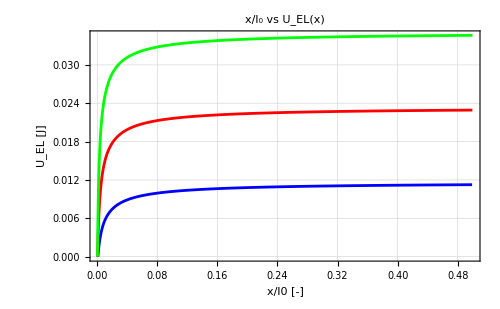
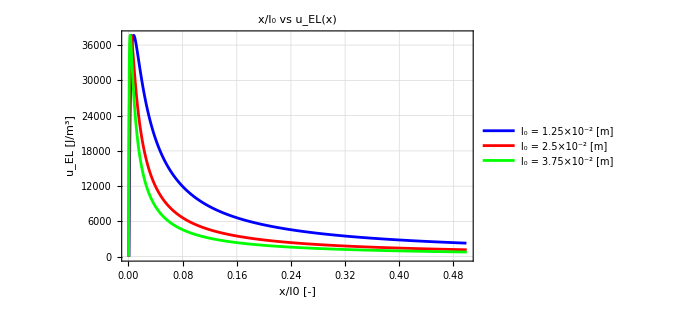

```mathematica
Row@{
Show[Table[
ListPlot[Transpose[{xrangenorm[[i]],Uelx[[i]]}],Joined->True,PlotStyle->colors[[i]]],{i,1,Length@l0range}],
PlotRange->All,Evaluate@opts,PlotLabel->"x/l_0 vs U_EL(x)",FrameLabel->{"x/l0 [-]","U_EL [J]"},ImageSize->500],Spacer@100,
Show[Table[
ListPlot[Transpose[{xrangenorm[[i]],uelx[[i]]}],PlotRange->All,Joined->True,PlotStyle->colors[[i]],PlotLegends->{l0strings[[i]]}],{i,1,Length@l0range}],
Evaluate@opts,PlotLabel->"x/l_0 vs u_EL(x)",FrameLabel->{"x/l0 [-]","u_EL [J/m^3]"},ImageSize->500]}
```

### Redefine x limits

```mathematica
xmax=0.3 l0/.l0->l0range/.celldata
```

{0.00375,0.0075,0.01125}

```mathematica
xrangeeff=Range[xmin,xmax,10^-5];
```

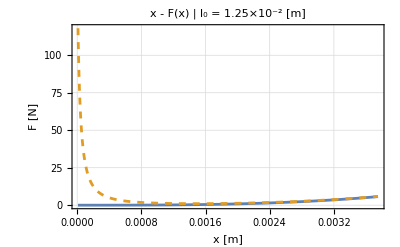
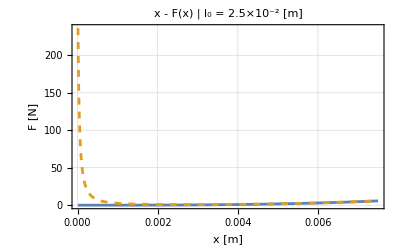
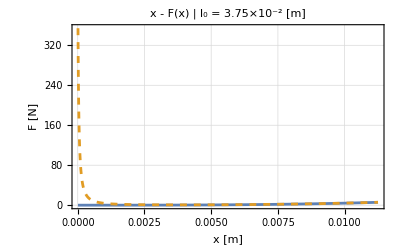

```mathematica
Row[
Flatten@Table[{
Plot[Evaluate@Table[Fpstrainl0[[i]]/.V->VV,{VV,{0,Vmaxl0[[i]]}}],{x,xmin,xmax[[i]]},PlotStyle->{Automatic,Dashed},Evaluate@opts,PlotRange->All,FrameLabel->{"x [m]","F [N]"},PlotLabel->StringJoin["x - F(x) | ",l0strings[[i]]],ImageSize->400],Spacer@20},
{i,1,Length@l0range}]]
```

### Q-V plots

```mathematica
Cvec=CC/.pstrain/.celldata/.x->xrange[[2]];
Vmaxvec=Vmax/.pstrain/.celldata/.x->xrange[[2]];
Qmaxvec=Cvec Vmaxvec;
```

```mathematica
VmaxofQQ=Interpolation[Transpose@{Qmaxvec,Vmaxvec}];
Qmaxlim=Flatten[VmaxofQQ["Domain"]][[2]]
QminlimVmax=Flatten[VmaxofQQ["Domain"]][[1]]
VmaxofQ[Q_]:=Piecewise[{{VmaxofQQ[Q], Between[Q,Flatten@VmaxofQQ["Domain"]]}, {-10^-50, Not@Between[1,Flatten@VmaxofQQ["Domain"]]}}]
```

7.51101×10^-6

1.68576×10^-7

Minimum strain -> C1 max, Maximum strain -> C1 min, C =Q/V, V  = Q/C, Q = C V

```mathematica
Cmin=CC/.pstrain/.celldata/.x->xmaxth
Cmax=CC/.pstrain/.celldata/.x->xmin
```

2.2707×10^-11

1.20182×10^-9

```mathematica
Vminstr[Q_]:=Q/Cmax;
Vmaxstr[Q_]:=Piecewise[{{Q/Cmin, Between[Q,{0,Flatten[VmaxofQQ["Domain"]][[1]]}]}, {-10^-50, Not@Between[Q,{0,Flatten[VmaxofQQ["Domain"]][[1]]}]}}];
```

```mathematica
Cminextr=(Flatten[VmaxofQQ["Domain"]][[1]])/VmaxofQ[Flatten[VmaxofQQ["Domain"]][[1]]]
```

2.73329×10^-11

```mathematica
Cminextr-Cmin
```

4.6259×10^-12

```mathematica
Vmaxstrextr[Q_]:=Piecewise[{{Q/Cminextr, Between[Q,{0,Flatten[VmaxofQQ["Domain"]][[1]]}]}, {-10^-50, Not@Between[Q,{0,Flatten[VmaxofQQ["Domain"]][[1]]}]}}];
```

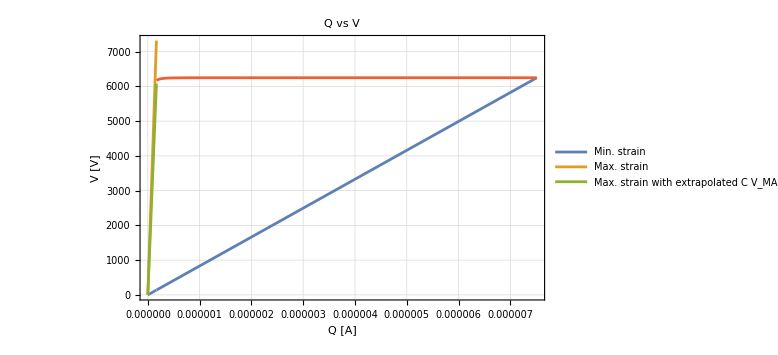

```mathematica
Plot[{Vminstr[Q],Vmaxstr[Q],Vmaxstrextr[Q],VmaxofQ[Q]},{Q,0,Qmaxlim},Evaluate@opts,PlotRange->{Automatic,{0,Automatic}},ImageSize->Large,FrameLabel->{"Q [A]","V [V]"},PlotLabel->"Q vs V",PlotLegends->{"Min. strain","Max. strain","Max. strain with extrapolated C""V_MAX"}]
```

```mathematica
VmaxofQ[Qmaxlim]==Vminstr/.Q->Qmaxlim
```

6249.71==Vminstr

```mathematica
VmaxofQ[Flatten[VmaxofQQ["Domain"]][[1]]]==Vmaxstr[Flatten[VmaxofQQ["Domain"]][[1]]]
```

False

```mathematica
VmaxofQ[Flatten[VmaxofQQ["Domain"]][[1]]]==Vmaxstrextr[Flatten[VmaxofQQ["Domain"]][[1]]]
```

True

```mathematica
UelQV=ParallelTable[NIntegrate[Vmaxstrextr[Q]+VmaxofQ[Q]-Vminstr[Q],{Q,0,Qfin}],{Qfin,0,Qmaxlim,5 10^-8}];
```

```mathematica
(*xofQ=Interpolation[Transpose@{(CC/.pstrain/.celldata)Vmax/.pstrain/.celldata/.x->xrange[[2]],xrange[[2]]}];
Qvectmp=LinSpace[QminlimVmax,Qmaxlim,Length@UelQV];
Show[
ListPlot[Transpose[{xrangenorm[[2]],Uelx[[2]]}],Joined->True],
ListPlot[Transpose[{Sort[Table[xofQ[Qvectmp[[QQ]]],{QQ,1,Length@Qvectmp}]]/l0range[[2]],UelQV}],Joined->True],
PlotRange->All,Evaluate@opts,PlotLabel->"x/l_0 vs U_EL(x)",FrameLabel->{"x/l0 [-]","U_EL [J]"},ImageSize->500]*)
```

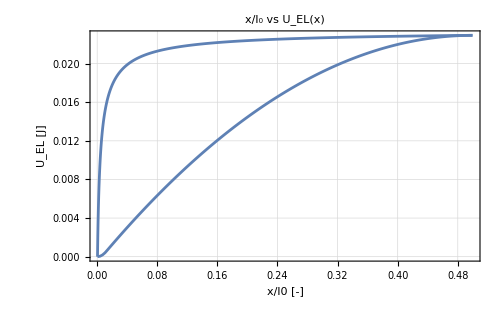

```mathematica
Show[
ListPlot[Transpose[{xrangenorm[[2]],Uelx[[2]]}],Joined->True],
ListPlot[Transpose[{LinSpace[xrangenorm[[2,1]],Last@xrangenorm[[2]],Length@UelQV],UelQV}],Joined->True],
PlotRange->All,Evaluate@opts,PlotLabel->"x/l_0 vs U_EL(x)",FrameLabel->{"x/l0 [-]","U_EL [J]"},ImageSize->500]
```

## Save

```mathematica
toexp=Association[
"tf"->tf,"l0range"->l0range,"w0range"->w0range,"tp0range"->tp0range,"ξ0range"->ξ0range,"xmin"->xmin,"xmaxth"->xmaxth,
"Vmax"->Vmax,
"PSTRAIN"->Association["pstraincond"->pstraincond,"geometry"->pstrain,"F"->Fpstrain,"xrange"->xrange,"Uelx"->Uelx[[2]],"uelx"->uelx[[2]]],
"PSTRESS"->Association["pstresscond"->pstresscond,"geometry"->pstress],
"NOSTRAIN"->Association["nostraincond"->nostraincond,"geometry"->nostrain]
];
```

```mathematica
Export["1DOF.m",toexp]
```

1DOF.m